```mathematica
ClearAll["Global`*"];
```

```mathematica
dat=ReadList["KBHSH3.dat",{Number,Number,Number,Number,Number,Number,Number}];
nx=251;ny=30;
xmax=dat[[251,1]];xmin=dat[[1,1]];
ymax=dat[[nx*ny,2]];ymin=dat[[1,2]];
rh=0.04;OmegaH=0.68;
```

```mathematica
cts =NSolve[OmegaH==Sqrt[x(x-rh)]/((rh-x)(rh-2x)),x];
ct=cts[[2,1,2]];
```

```mathematica
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2/M
a/M
RH = M+Sqrt[M^2-a^2];
```

0.715006

0.714727

0.999609

```mathematica
Xtor[X_]:=If[X≠1,Sqrt[(X/(1-X))^2],1000]
```

```mathematica
f1=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,3]]]},{i,1,ny},{j,1,nx}];
f2=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,4]]]},{i,1,ny},{j,1,nx}];
f0=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,5]]]},{i,1,ny},{j,1,nx}];
W=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,7]]},{i,1,ny},{j,1,nx}];
H[r_]:=1-rh/r;
```

```mathematica
(*f1[[ny,All,2]] = N[π/2,5] ;(* mathematica being silly... *)
f1[[ny,All,2]]*)
```

```mathematica
if1=Interpolation[Flatten[f1,1],InterpolationOrder->4];
if2=Interpolation[Flatten[f2,1],InterpolationOrder->4];
if0=Interpolation[Flatten[f0,1],InterpolationOrder->4];
iW=Interpolation[Flatten[W,1],InterpolationOrder->4];
```

```mathematica
f1 = if1;
f2=if2;
f0=if0;
W=iW;
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=+f2[r,θ]*r^2*Sin[θ]^2W[r,θ];

metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_] := R - a^2/RH;
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coords[[k]]]+D[metric[[s,k]],coords[[j]]]-D[metric[[j,k]],coords[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] coords[[j]]' coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.05*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler 
I want to plot in the R, i.e. BL, radial coordinates, so for solution 1, I have to translate to R via r = R - a^2/RH *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=(r[τ]+a^2/RH) Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=(r[τ]+a^2/RH) Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=(r[τ]+a^2/RH) Cos[θ[τ]]/.soln;{xs,ys,zs}]
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
If[mτ==τend,color=Hue[hue],color=Black];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->color]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
If[mτ==τend,color=Hue[hue],color=Black];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->color]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
If[mτ==τend,color=Hue[hue],color=Black];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->color]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
If[mτ==τend,color=Hue[hue],color=Black];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->color]]
```

```mathematica
bottom = 0.0041;
top=0.0044;
left=0.001;
right=0.003;
dr=-0.15;
τend=.;uinvar = 0;
rplus=M+Sqrt[M^2-a^2];
ics={0,12,π/2,0};
horizpl2D=PolarPlot[rh+a^2/RH,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Red,Thick}];
horizpl3D=SphericalPlot3D[{rh+a^2/RH,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity,PlotPoints->50];
τPlot=250;
dθs={0,bottom/10,bottom/4,bottom/2,3 bottom/4,4bottom/5,0.00415,0.0042,top,5/4 top};
dθs={bottom/10,3 bottom/4,0.00415};
dϕ=(right+left)/2;
```

```mathematica
xyPlots = {};
xzPlots = {};
yzPlots = {};
xyzPlots = {};
Do[
dθ=dθs[[i]];
ivs = {dr,dθ,dϕ};
hue=i/Length[dθs];
soln = computeSoln[τPlot,ivs,ics];
xyz=sphslnToCartsln[soln];
If[τPlot==τend,Print["The particle did not cross the horizon for initial coordinates=",ics," and initial velocities=",ivs],Print["For initial coordinates=",ics," and initial velocities=",ivs," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
If[τPlot==τend,color=Hue[hue],color=Black];
xyPlot =ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->color];
xyPlots = AppendTo[xyPlots,xyPlot];
xzPlot = ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->color];
xzPlots = AppendTo[xzPlots,xzPlot];
yzPlot = ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->color];
yzPlots = AppendTo[yzPlots,yzPlot];
xyzPlot= ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->color];
xyzPlots = AppendTo[xyzPlots,xyzPlot];
,{i,1,Length[dθs]}]
```

InterpolatingFunction::dmval: Input value {11.9649, 1.57089} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.00041,0.002} the particle crosses the horizon at τend=75.1011

With final coordinates={t = 35.5637,r = 0.042,θ = 1.57581,ϕ = -1.40869}

The particle did not cross the horizon for initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.003075,0.002}

With final coordinates={t = 289.893,r = 4.77434,θ = 1.28177,ϕ = -7.10906}

For initial coordinates={0,12,π/2,0} and initial velocities={-0.15,0.00415,0.002} the particle crosses the horizon at τend=93.132

With final coordinates={t = 47.2119,r = 0.042,θ = 1.13884,ϕ = 1.39518}

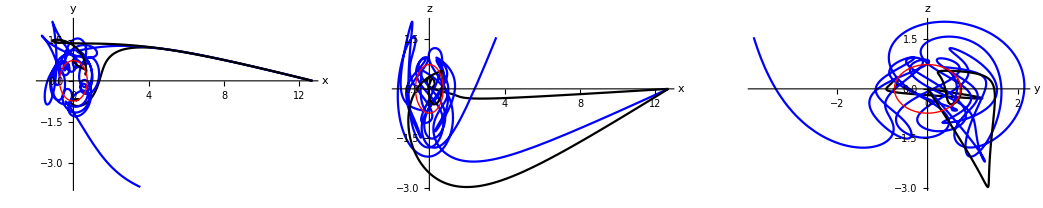

```mathematica
(*GraphicsGrid[{{Show[xyPlots,horizpl2D]
,Show[xzPlots,horizpl2D]}
,{Show[yzPlots,horizpl2D]
,Show[xyzPlots,horizpl3D]}}]*)
GraphicsRow[{Show[xyPlots,horizpl2D],
Show[xzPlots,horizpl2D],
Show[yzPlots,horizpl2D]}]
Show[xyzPlots,horizpl3D]
```